```mathematica
E^(18*I*Pi/4)
```

ⅈ

```mathematica
M = {{1,1,1,1},{1,I,-1,-I},{1,-1,1,-1},{1,-I,-1,I}}
```

{{1,1,1,1},{1,ⅈ,-1,-ⅈ},{1,-1,1,-1},{1,-ⅈ,-1,ⅈ}}

```mathematica
M
```

{{1,1,1,1},{1,ⅈ,-1,-ⅈ},{1,-1,1,-1},{1,-ⅈ,-1,ⅈ}}

```mathematica
M//MatrixForm
```

(1 | 1 | 1 | 1
1 | ⅈ | -1 | -ⅈ
1 | -1 | 1 | -1
1 | -ⅈ | -1 | ⅈ)

```mathematica
Norm[M.{1,0,0,1}]
```

2 √2

```mathematica
w = Sqrt[I]
```

(-1)^(1/4)

```mathematica
U = {
{1,1,1,1,1,1,1,1},
{1,w^1,w^2,w^3,w^4,w^5,w^6,w^7},
{1,w^2,w^4,w^6,w^8,w^2,w^4,w^6},
{1,w^3,w^6,w^1,w^4,w^7,w^2,w^5},
{1,w^4,w^8,w^4,w^8,w^4,w^8,w^4},
{1,w^5,w^2,w^7,w^4,w^1,w^6,w^3},
{1,w^6,w^4,w^2,w^8,w^6,w^4,w^2},
{1,w^7,w^6,w^5,w^4,w^3,w^2,w^1}
};
```

```mathematica
U//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4)
1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ
1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4)
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4)
1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ
1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4))

```mathematica
U.{1,0,1,0,1,0,1,0}//Simplify
```

{4,0,0,0,4,0,0,0}

```mathematica
U.{0,1,0,1,0,1,0,1}//Simplify
```

{4,0,0,0,-4,0,0,0}

```mathematica
U.{1,0,0,1,0,0,1,0}//Simplify
```

{3,(1-ⅈ)+(-1)^(3/4),-ⅈ,(1+ⅈ)+(-1)^(1/4),1,(1-ⅈ)-(-1)^(3/4),ⅈ,(1+ⅈ)-(-1)^(1/4)}

```mathematica
U.{0,1,0,0,1,0,0,1}*U.{0,1,0,0,1,0,0,1}//Simplify
```

{9,3-2 √2,1,3+2 √2,1,3+2 √2,1,3-2 √2}

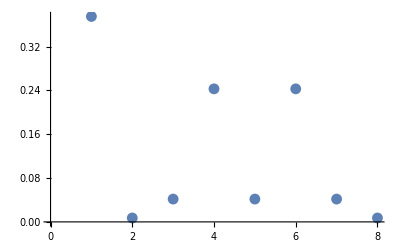

```mathematica
ListPlot[U.{1,0,0,1,0,0,1,0}*Conjugate[U.{1,0,0,1,0,0,1,0}]/24]
```